23rd of August 2020
This is a short programme which will look at plotting the logistic equation.

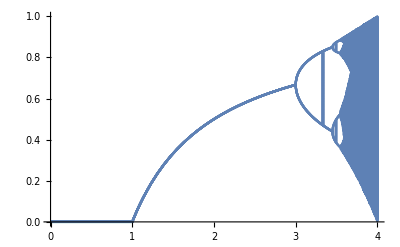

```mathematica
Remove[x,y,r]
G[r_,xi_,N_]:=
RecurrenceTable[{x[n+1]==r*x[n]*(1-x[n]),x[0]==xi},x,{n,0,N}]

G[3,0.9,100];
PlotLogisticmap[N_,xi_,M_]:=
Plot[{G[r,xi,N][[N-#]]&/@{Range[14]}},{r,0,M},PlotStyle->"Blue"]

(*Now we can try and plotting all the branches *)
Tally[N[G[3.2,0.1,10000],3]];

PlotLogisticmap[10000,0.1,4] (*Make the first number low for high-res low res logistic map, 10 is best number*)
```